```mathematica
Import[FileNameJoin[{NotebookDirectory[],"modules/breed.m"}]];
Import[FileNameJoin[{NotebookDirectory[],"modules/fitfunctions.m"}]];
Import[FileNameJoin[{NotebookDirectory[],"modules/generators.m"}]];
Import[FileNameJoin[{NotebookDirectory[],"modules/gielis.m"}]];
Import[FileNameJoin[{NotebookDirectory[],"modules/helpers.m"}]];
Import [FileNameJoin[{NotebookDirectory[],"modules/phenotypes.m"}]];
```

# Script Start

```mathematica
(*Input Data*)
(*imgData=Import[SystemDialogInput["FileOpen"]];*)
orignalImg = Import[FileNameJoin[{NotebookDirectory[],"ball2.png"}]]
orignalImgDim  = ImageDimensions[orignalImg]
imgData = CropX[orignalImg];
imgDataPixels = PixelValuePositions[imgData,Black,0.5];
imgDataPixelsMirrored = Map[{#⟦1⟧, -#⟦2⟧}&,imgDataPixels];
allImageFitness = {};
allDistanceFitness = {};

(*Live Data Variables*)
fitnessPlots=Null;Dynamic[fitnessPlots]
text = Null; Dynamic[text]
timingText= Null; Dynamic[timingText]
allImages = Null; Dynamic[allImages]
fittestHistory = {}; Dynamic[fittestHistory]
fittestPhenotype = {}; Dynamic[fittestPhenotype]

(*Algorithm Related Parameters*)
fittestIndex = -1;
showPopulation = False;
currentStep =0;
nsteps = 50000;
updatePlotsRate = 50;
gaussianparam = {5,3};

(*Biological Structure Parameters*)
numGenoms  = 10;
resolution = 10;
gielisPoints = 200;

(*Mutation Parameters*)
nextGenFrac = 0.5;
pcross = 1;
pEliteBreed = 0.1;
pmut = 0.01;
pMutElite = 0.01;

paramRanges={
{0.1,2}, (*a*)
{0.1,2},(*b*)
{-10,10},(*m1*)
{-10,10},(*m2*)
{1,20},(*n1*)
{-20,20},(*n2*)
{-20,20}(*n3*)
}; 

(*Calculated Configuration*)
replaceN = IntegerPart[numGenoms*nextGenFrac];
imgDim = ImageDimensions[imgData];

(*setup debug variables*)
imgDataPixels⟦1 ;; Length[imgDataPixels], 1⟧= imgDataPixels⟦1 ;; Length[imgDataPixels], 1⟧ - imgDim⟦1⟧/2;
imgDataPixelsMirrored⟦1 ;; Length[imgDataPixelsMirrored], 1⟧= imgDataPixelsMirrored⟦1 ;; Length[imgDataPixelsMirrored], 1⟧ - imgDim⟦1⟧/2;
totalFitness = Table[0,{i,1,nsteps}];
maxFitness = Table[0,{i,1,nsteps}];

genotypeLength = 7*resolution;
ffitfunc = GielisFFitGen[imgData, gaussianparam];

(*Start, Beginning of Evolution*)
genotypes = BinPopGenerator [numGenoms,genotypeLength];
```

-Graphics-

{200,100}

```mathematica
outDir = FileNameJoin[{NotebookDirectory[],"sim/current"}];
If[!DirectoryQ[outDir], CreateDirectory[outDir]];
Do[Module[{isEliteBreed, eliteList, mutationList},
isEliteBreed = RandomReal[]<pEliteBreed;

timeTotal = AbsoluteTime[];

timefitness = AbsoluteTiming[
phenotypes = Table[Module[{params, points},
params = GielisPhenotype[genotypes⟦i⟧,resolution, paramRanges ];
points = GielisScaled[gielisPoints,{-imgDim⟦1⟧/2,imgDim⟦1⟧/2}, params]
(*points = GielisOffset[gielisPoints, params]*)
], {i, 1,numGenoms}];

imageFitness = Table[ffitfunc[ phenotypes⟦i⟧],{i, 1,numGenoms}];
AppendTo[allImageFitness, imageFitness];
distanceFitness = Table[Module[{distances, quantile},
distances = Table[EuclideanDistance [ phenotypes⟦genom,i-1⟧,phenotypes⟦genom,i⟧],{i,2,gielisPoints}];
quantile = Quantile[distances,1/4];
Logistic[quantile]
],{genom, 1, numGenoms}];
AppendTo[allDistanceFitness, distanceFitness];
fitness = MapThread[#1*#2 &,{imageFitness, distanceFitness}]
];
timeBreed = AbsoluteTiming[
If[isEliteBreed,
p1Index = Ordering[fitness,-1]⟦1⟧;
p2Index = Ordering[fitness,-2]⟦1⟧;,
p1Index=SelectParentByWheel[genotypes, fitness];
p2Index=SelectParentByWheel[genotypes, fitness];
];
p1 = genotypes⟦p1Index⟧;
p2 = genotypes⟦p2Index⟧;
lowestN = Ordering[fitness,replaceN];
children = Table[ BreedDoubleCross [p1, p2, genotypeLength, pcross],{i,1,replaceN}];
Do[genotypes⟦lowestN⟦i⟧⟧ = children⟦i⟧;, {i,1,replaceN}];

mutateN = numGenoms-2;
mutationList =  Ordering[fitness,mutateN];
eliteList = Ordering[fitness,mutateN];
Do[genotypes⟦eliteList⟦i⟧⟧= Mutate[genotypes⟦eliteList⟦i⟧⟧, genotypeLength, pMutElite], {i,1,2}];
Do[genotypes⟦mutationList⟦i⟧⟧= Mutate[genotypes⟦mutationList⟦i⟧⟧, genotypeLength, pmut], {i,1,mutateN}];
];

timeEvaluate = AbsoluteTiming[
maxFitness⟦iteration⟧ = Max[fitness];
totalFitness⟦iteration⟧ = Fold[Plus,0,fitness] ;

If[Mod[iteration,updatePlotsRate] == 0,
params =  Table[GielisPhenotype[genotypes⟦i⟧,resolution, paramRanges ],{i, 1,numGenoms}];
csv = ExportString[params,"RawJSON"];
Export[FileNameJoin[{outDir,StringJoin["phenotypes-", ToString[iteration],".txt"]}],csv];

fitnessPlots = Grid[{
{ListPlot[totalFitness⟦1 ;; iteration⟧,
ImageSize->Medium ,
PlotLabel->"Generation Total", 
AxesLabel->{"Step", "Fitness"} ],
ListPlot[maxFitness⟦1 ;; iteration⟧,
ImageSize->Medium,
PlotLabel->"Maximum", 
AxesLabel->{"Step", "Fitness"}]}
}];
];

If[showPopulation || Mod[iteration,updatePlotsRate] == 0,
allImages = Table[ListPlot[phenotypes⟦i⟧, ImageSize->imgDim],{i,1,numGenoms}];
];

If[Ordering[fitness,-1]⟦1⟧  ≠ fittestIndex, 
fittestIndex = Ordering[fitness,-1]⟦1⟧;
fittestHistory = ResultPlot[imgDataPixels, imgDataPixelsMirrored,phenotypes⟦fittestIndex⟧ ,imgDim, True];
fittestPhenotype = GielisPhenotype[genotypes⟦fittestIndex⟧,resolution, paramRanges ];
];
];

timeTotal = AbsoluteTime[]-timeTotal; 
text = ExportString[{{"Step: ",iteration, " of ",nsteps," ", "Parents:",p1Index, p2Index ,"EliteProcess:",isEliteBreed}},"Table"];
timingText =ExportString[ {{"T_ffit:", timefitness⟦1⟧},{"T_Eval:", timeEvaluate⟦1⟧},{"T_Breed:",timeBreed⟦1⟧},{ "T_total:",timeTotal}},"Table"];
currentStep =iteration;
], {iteration, 1,nsteps}
];
```

$Aborted

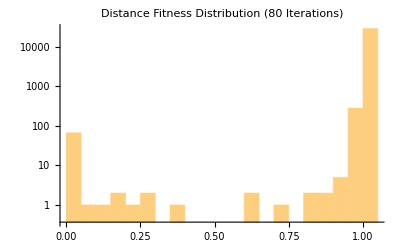

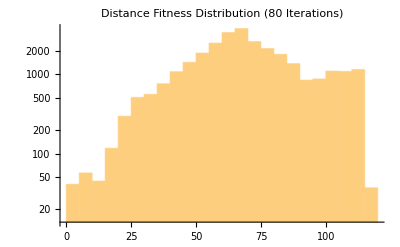

```mathematica
Histogram[Flatten[allDistanceFitness], ScalingFunctions->"Log", PlotLabel->"Distance Fitness Distribution (80 Iterations)"]
Histogram[Flatten[allImageFitness], ScalingFunctions->"Log", PlotLabel->"Distance Fitness Distribution (80 Iterations)"]
```

# Exporting Data

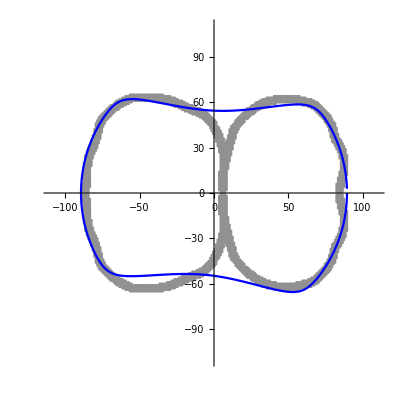

Export Success

```mathematica
outDir = FileNameJoin[{NotebookDirectory[],"results/monday/ball5"}];
title = "Performance Using Double Crossing";
If[!DirectoryQ[outDir], Module[{totFitPlot, maxFitPlot,fittestPlot,fittestPlotMarkers, variables,
meanFits, smoothMeanFit, smoothMeanFits , avgFitnessPlot,smoothAvgFitnessPlot,  fourierPlot, smoothFourierPlot,
d2results, fitness, meanFit, densityHistogramPlot},
totFitPlot = ListPlot[totalFitness⟦1 ;; currentStep⟧,
ImageSize->Large ,
PlotLabel->"Generation Total", 
PlotRange->All,
AxesLabel->{"Step", "Fitness"}];
maxFitPlot = ListPlot[maxFitness⟦1 ;; currentStep⟧,
ImageSize->Large,
PlotLabel->"Maximum",
PlotRange->All,
 AxesLabel->{"Step", "Fitness"}];
fittestPlot = ResultPlot[imgDataPixels, imgDataPixelsMirrored,phenotypes⟦fittestIndex⟧ ,orignalImgDim , False];
fittestPlotMarkers = ResultPlot[imgDataPixels, imgDataPixelsMirrored,phenotypes⟦fittestIndex⟧ ,orignalImgDim, True];
CreateDirectory[outDir];
variables =ExportString[{
{"Title", title},
{"numGenoms", numGenoms},
{"resolution", resolution},
{"gielisPoints", gielisPoints},
{"nextGenFrac", nextGenFrac},
{"pcross", pcross},
{"pEliteBreed", pEliteBreed},
{"pmut", pmut},
{"pMutElite", pMutElite},
{"gaussianparam", gaussianparam}
}, "Table"];

d2results = MapThread[{#2,#1} &,{Flatten[allDistanceFitness], Flatten[allImageFitness]}];
fitness = MapThread[#1*#2 &,{allDistanceFitness, allImageFitness}];
meanFit = Map[Mean[#1] &, fitness];
meanFits=meanFit⟦100;;Length[meanFit]⟧-Mean[meanFit⟦100;;Length[meanFit]⟧];
smoothMeanFit= MovingAverage[meanFit,10];
smoothMeanFits = smoothMeanFit⟦100;;Length[smoothMeanFit]⟧-Mean[smoothMeanFit⟦100;;Length[smoothMeanFit]⟧];

avgFitnessPlot = ListLinePlot[meanFits,
PlotRange->{{0,Length[meanFit]},All}, 
ImageSize->Large];
smoothAvgFitnessPlot = ListLinePlot[smoothMeanFits,
ImageSize->Large,
PlotRange->{{0,Length[meanFit]},All},
 AxesLabel->{"Step", "Mean"}];
fourierPlot = ListPlot[Abs[Fourier[meanFits]],
ImageSize->Large,
PlotRange->{All,All},Joined->True];
smoothFourierPlot = ListPlot[MovingAverage[Abs[Fourier[smoothMeanFits]],5],
ImageSize->Large,
PlotRange->{{0,Length[meanFit]/2},All},
Joined->True,AxesLabel->{"w", OverHat["f(w)"]} ];

densityHistogramPlot = DensityHistogram[d2results, 
ImageSize-> Medium,
PlotLabel->"2D Fitness Distribution",
Method->{"DistributionAxes"->"Histogram"}];

Export[ FileNameJoin[{outDir,"densityHistogramPlot.png"}],densityHistogramPlot];
Export[ FileNameJoin[{outDir,"avgFitnessPlot.png"}],avgFitnessPlot];
Export[ FileNameJoin[{outDir,"smoothAvgFitnessPlot.png"}],smoothAvgFitnessPlot];
Export[ FileNameJoin[{outDir,"fourierPlot.png"}],fourierPlot];
Export[ FileNameJoin[{outDir,"smoothFourierPlot.png"}],smoothFourierPlot];

Export[FileNameJoin[{outDir,StringJoin[title,".txt"]}],variables];
Export[ FileNameJoin[{outDir,"totFitPlot.png"}],totFitPlot];
Export[ FileNameJoin[{outDir,"maxFitPlot.png"}],maxFitPlot];
Export[ FileNameJoin[{outDir,"fittestPlot.png"}],fittestPlot];
Export[ FileNameJoin[{outDir,"fittestPlotMarkers.png"}],fittestPlotMarkers];
Print[fittestPlot];
Print["Export Success"];
],
Print["Directory already exists! Choose a different file name"]
];
```

# Visualize Curves

```mathematica
(*pin=  GielisPhenotype[genotypes⟦fittestIndex⟧,resolution, paramRanges ];*)
pin = {0.760547,0.857031,4.97949,3.8457,13.3945,9.72656,3.20313};
Manipulate[Module[{},
gs = GielisScaled[1000,{-imgDim⟦1⟧/2,imgDim⟦1⟧/2},{a,b,m1,m2,n1,n2,n3}];
distances = Table[EuclideanDistance [ gs⟦i-1⟧,gs⟦i⟧],{i,2,Length[gs]}];
Grid[{
{ListPlot[gs,ImageSize-> Large]},
 {Logistic[Quantile[distances,1/2]]},
{{a,b,m1,m2,n1,n2,n3}}

}]],
{{a,pin⟦1⟧, "a"}, paramRanges⟦1,1⟧, paramRanges⟦1,2⟧},
{{b,pin⟦2⟧, "b"},  paramRanges⟦2,1⟧, paramRanges⟦2,2⟧},
{{m1,pin⟦3⟧, "m1"},  paramRanges⟦3,1⟧, paramRanges⟦3,2⟧},
{{m2,pin⟦4⟧, "m2"},  paramRanges⟦4,1⟧, paramRanges⟦4,2⟧},
{{n1,pin⟦5⟧, "n1"},  paramRanges⟦5,1⟧, paramRanges⟦5,2⟧},
{{n2,pin⟦6⟧, "n2"},  paramRanges⟦6,1⟧, paramRanges⟦6,2⟧},
{{n3,pin⟦7⟧, "n3"}, paramRanges⟦7,1⟧, paramRanges⟦7,2⟧}]
```

# Save Curve as PNG

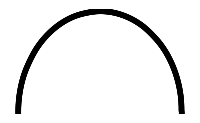

```mathematica
outName = FileNameJoin[{NotebookDirectory[],"elipse.png"}];
params ={1.455,1.582,14.47,4.470000000000001,3.95,12.100000000000001,0.};
gs = GielisScaled[1000,{-imgDim⟦1⟧/2,imgDim⟦1⟧/2},params];
marker=Graphics[{Black,Disk[]}];
img = ListPlot[gs,ImageSize-> imgDim, Axes-> False,PlotRange->{{-imgDim⟦1⟧/2,imgDim⟦1⟧/2},{0,imgDim⟦2⟧}}, PlotStyle->Black, PlotMarkers->{marker, .03}]
If[!FileExistsQ[outName],Export[outName,img], Print["Could not store the file: file exists"]];
```

```mathematica
imgDim
```

{162,200}

```mathematica
imgData
```

-Graphics-